# Conos de luz

```mathematica
Clear["Global`*"]
```

## Schwarzschild 5D

### Observador dentro del agujero negro

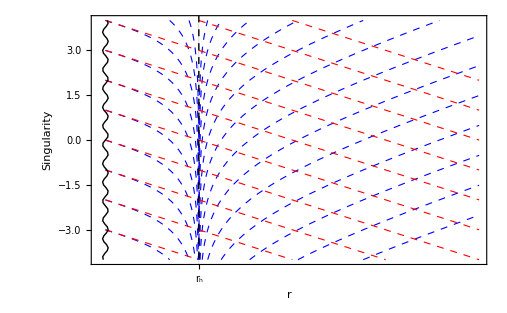

```mathematica
μ=1;
rh=Sqrt[μ];
tin[r_,c_]:=c-r;

tout[r_,c_]:=c+r+rh*Log[Abs[(r-rh)/(r+rh)]];
cs=Range[-6,6,1];
singularity=Table[{0.03*Sin[10 t],t},{t,-4,4,0.1}];
Sch5Din=Plot[Evaluate[Join[Table[tout[r,c],{c,cs}],Table[tin[r,c],{c,cs}]]],{r,0,4},Exclusions->{r==rh},PlotRange->{{0-0.07,4},{-4,4}},Axes->False,Frame->True,BaseStyle->{FontFamily->"Times"},LabelStyle->Directive[FontSize->16],FrameLabel->{Style[TraditionalForm[r],18],Style[Style[TraditionalForm[Singularity],18]]},FrameTicks->{{None,None},{{{rh,Style["r_h",12]}},None}},PlotStyle->Join[Table[{Directive[Blue,Dashed,AbsoluteThickness[0.8]]},{Length[cs]}],Table[{Directive[Red,Dashed,AbsoluteThickness[0.8]]},{Length[cs]}]],GridLines->{{rh},None},Epilog->{{Black,Thick,Line[singularity]},{Black,Dashed,Thick,InfiniteLine[{{rh,0},{rh,1}}]}}]
```

```mathematica
Export["Sch5Din.png",Sch5Din]
```

Sch5Din.png

### Observador fuera del agujero negro

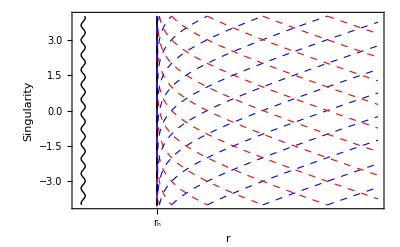

```mathematica
μ:=1
rh:=Sqrt[μ]
rStar[r_]:=r+(rh/2)*Log[Abs[(r-rh)/(r+rh)]];

(*Trayectorias de luz en Schwarzschild 5D(t vs r)*)
(*t=constant\pm r**)
Sch5Dout=Plot[Evaluate[Table[{rStar[r]+c,-rStar[r]+c},{c,-20,20,1}]],{r,rh,4},Exclusions->{r==rh},PlotRange->{{0-0.07,4},{-4,4}},Axes->False,Frame->True,BaseStyle->{FontFamily->"Times"},LabelStyle->Directive[FontSize->16],FrameLabel->{Style[TraditionalForm[r],18],Style[TraditionalForm[Singularity],18]},FrameTicks->{{None,None},{{{rh,Style["r_h",12]}},None}},PlotStyle->Flatten[Table[{Directive[Blue,Dashed,AbsoluteThickness[0.8]],Directive[Red,Dashed,AbsoluteThickness[0.8]]},{c,-20,20,1}],1],GridLines->{{rh},None},Epilog->{{Black,Thick,Line[singularity]},{Black,Dashed,Thick,InfiniteLine[{{rh,0},{rh,1}}]}}]
```

```mathematica
Export["Sch5Dout.png",Sch5Dout]
```

Sch5Dout.png

## Gauss-Bonnet 5D

### Observador dentro del agujero negro

0.707107

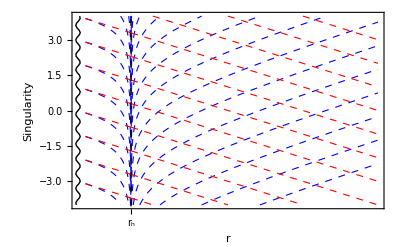

```mathematica
μ=2;

(*Integrando*)
Int[r_?NumericQ]:=(1-r^2+Sqrt[r^4+μ])/(1+r^2-Sqrt[r^4+μ]);

(*Horizonte*)
rh=r/. FindRoot[1+r^2-Sqrt[r^4+μ]==0,{r,1}]//N

(*Coordenadas nulas*)
tin[r_,c_]:=c-r;

tout[r_?NumericQ,c_]:=Module[{eps=10^-5},Which[r<rh-eps,c+NIntegrate[Int[s],{s,0,r},Method->"GlobalAdaptive",MaxRecursion->20],r>rh+eps,c+NIntegrate[Int[s],{s,0,rh-eps},Method->"GlobalAdaptive",MaxRecursion->20]+NIntegrate[Int[s],{s,rh+eps,r},Method->"GlobalAdaptive",MaxRecursion->20],True,Indeterminate]]

(*Constantes*)
cs=Range[-6,10,1];

(*Singularidad (r≈0)*)
singularity=Table[{0.03*Sin[10 t],t},{t,-4,4,0.1}];

(*Gráfico*)
GB5Din=Plot[Evaluate@Join[Table[tout[r,c],{c,cs}],Table[tin[r,c],{c,cs}]],{r,0.1,4},Exclusions->{r==rh},PlotRange->{-4,4},Axes->False,Frame->True,BaseStyle->{FontFamily->"Times"},LabelStyle->Directive[FontSize->16],FrameLabel->{Style[TraditionalForm[r],18],Style[TraditionalForm[Singularity],18]},FrameTicks->{{None,None},{{{rh,Style["\!\(\*SubscriptBox[\(r\), \(h\)]\)",12]}},None}},PlotStyle->Join[Table[{Directive[Blue,Dashed,AbsoluteThickness[0.8]]},{Length[cs]}],Table[{Directive[Red,Dashed,AbsoluteThickness[0.8]]},{Length[cs]}]],GridLines->{{rh},None},Epilog->{{Black,Thick,Line[singularity]},{Black,Dashed,Thick,InfiniteLine[{{rh,0},{rh,1}}]}}]
```

```mathematica
Export["GB5Din.png",GB5Din]
```

GB5Din.png

### Observador fuera del agujero negro

0.707107

InterpolatingFunction::dmval: Input value {0.0000817143} lies outside the range of data in the interpolating function. Extrapolation will be used.

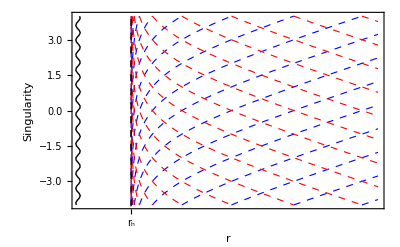

```mathematica
μ=2;
rh=r/.FindRoot[1+r^2-Sqrt[r^4+μ]==0,{r,1}]
(*Coordenada tortuga como solución de EDO*)
rStarFunc=NDSolveValue[{y'[r]==1/(1+r^2-Sqrt[r^4+μ]),y[rh+0.001]==0},y,{r,rh+0.000001,10},MaxStepSize->0.01];
(*Rayos de luz:t=±r*+c*)
GB5Dout=Plot[Evaluate[Table[{rStarFunc[r]+c,-rStarFunc[r]+c},{c,-15,15,1}]],{r,0,4},Exclusions->{r==rh},PlotRange->{-4,4},Axes->False,Frame->True,BaseStyle->{FontFamily->"Times"},LabelStyle->Directive[FontSize->16],FrameLabel->{Style[TraditionalForm[r],18],Style[Style[TraditionalForm[Singularity],18]]},FrameTicks->{{None,None},{{{rh,Style["r_h",12]}},None}},PlotStyle->Flatten[Table[{Directive[Blue,Dashed,AbsoluteThickness[0.8]],Directive[Red,Dashed,AbsoluteThickness[0.8]]},{c,-20,20,1}],1],Epilog->{{Black,Thick,Line[singularity]},{Black,Dashed,Thick,InfiniteLine[{{rh,0},{rh,1}}]}}]
```

```mathematica
Export["GB5Dout.png",GB5Dout]
```

GB5Dout.png

## Tercer orden 5D

### Observador dentro del agujero negro

```mathematica
μ=2;

f[r_]:=1+(r-2)^2-(101 (r-2)^4)/(7^(1/3) (-1085 (r-2)^6-1134 (r-2)^2 μ+18 √7 (r-2)^2 √(3699 (r-2)^8+1085 (r-2)^4 μ+567 μ^2))^(1/3))+1/7 (-7595 (r-2)^6-7938 (r-2)^2 μ+126 √7 (r-2)^2 √(3699 (r-2)^8+1085 (r-2)^4 μ+567 μ^2))^(1/3)
(*Integrando*)
Int[r_?NumericQ]:=(2/f[r])-1;

(*Horizonte*)
horizons=Select[r/. NSolve[f[r]==0,r],Im[#]==0&&0<Re[#]<10&]//Re;

{rInner,rOuter}=Sort[horizons]

(*Coordenadas nulas*)
tin[r_]:=-r;

eps=10^-4;
tout[r_?NumericQ]:=Module[{},Which[r<rInner-eps,NIntegrate[Int[s],{s,0.1,r}],rInner+eps<r<rOuter-eps,NIntegrate[Int[s],{s,rInner+eps,r}],r>rOuter+eps,NIntegrate[Int[s],{s,rOuter+eps,r}],True,Indeterminate]]

(*Constantes*)
cs=Range[-20,20,1];

(*Singularidad (r≈0)*)
singularity=Table[{0.03*Sin[10 t],t},{t,-4,4,0.1}];
```

{0.612933,3.38707}

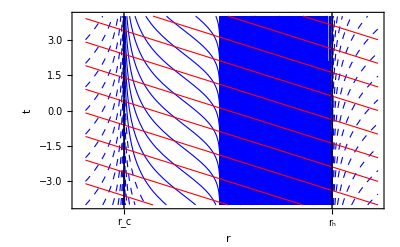

```mathematica
(*Gráfico*)
F35Din=Plot[Evaluate@Join[Table[c+tout[r],{c,cs}],Table[c+tin[r],{c,cs}]],{r,0.1,4},Exclusions->{r==rInner,r==rOuter},PlotRange->{-4,4},Axes->False,Frame->True,BaseStyle->{FontFamily->"Times"},LabelStyle->Directive[FontSize->16],FrameLabel->{Style[TraditionalForm[r],18],Style[TraditionalForm[t],18]},FrameTicks->{{None,None},{{{rInner,Style["\!\(\*SubscriptBox[\(r\), \(c\)]\)",12]},{rOuter,Style["\!\(\*SubscriptBox[\(r\), \(h\)]\)",12]}},None}},GridLines->{{rInner,rOuter},None},PlotStyle->Join[Table[{Directive[Blue,Dashed,AbsoluteThickness[0.8]]},{Length[cs]}],Table[{Directive[Red,Dashed,AbsoluteThickness[0.8]]},{Length[cs]}]],Epilog->{{Black,Dashed,Thick,InfiniteLine[{{rInner,0},{rInner,1}}]},{Black,Dashed,Thick,InfiniteLine[{{rOuter,0},{rOuter,1}}]}}]
```

```mathematica
Export["F35Din.png",F35Din]
```

F35Din.png

### Observador fuera del agujero negro

{0.153958,0.954716}

InterpolatingFunction::dmval: Input value {0.0000817143} lies outside the range of data in the interpolating function. Extrapolation will be used.

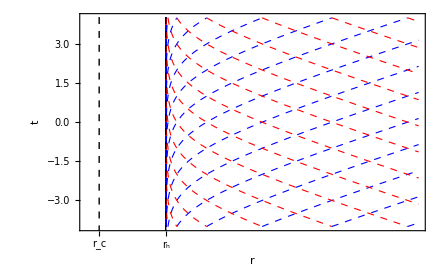

```mathematica
μ=1;

(*Función métrica de tercer orden*)
f[r_]:=1+r^2-(101 r^4)/(7^(1/3) (-1085 r^6-1134 r^2 μ+18 √7 r^2 √(3699 r^8+1085 r^4 μ+567 μ^2))^(1/3))+1/7 (-7595 r^6-7938 r^2 μ+126 √7 r^2 √(3699 r^8+1085 r^4 μ+567 μ^2))^(1/3)
(*Buscar ambas raíces*)
horizons=r/. NSolve[f[r]==0&&r<10&&r>0,r,Reals];
{rInner,rOuter}=Sort[horizons]
rStarExt=NDSolveValue[{y'[r]==1/f[r],y[rOuter+0.001]==0},y,{r,rOuter+0.001,10}];
F35Dout=Plot[Evaluate[Table[{rStarExt[r]+c,-rStarExt[r]+c},{c,-15,15,1}]],{r,0,4},Exclusions->{r==rh},PlotRange->{-4,4},Axes->False,Frame->True,BaseStyle->{FontFamily->"Times"},LabelStyle->Directive[FontSize->16],FrameLabel->{Style[TraditionalForm[r],18],Style[Style[TraditionalForm[t],18]]},FrameTicks->{{None,None},{{{rInner,Style["\!\(\*SubscriptBox[\(r\), \(c\)]\)",12]},{rOuter,Style["\!\(\*SubscriptBox[\(r\), \(h\)]\)",12]}},None}},PlotStyle->Flatten[Table[{Directive[Blue,Dashed,AbsoluteThickness[0.8]],Directive[Red,Dashed,AbsoluteThickness[0.8]]},{c,-20,20,1}],1],Epilog->{{Black,Dashed,Thick,InfiniteLine[{{rInner,0},{rInner,1}}]},{Black,Dashed,Thick,InfiniteLine[{{rOuter,0},{rOuter,1}}]}}]
```

```mathematica
Export["F35Dout.png",F35Dout]
```

F35Dout.png